Министерство образования и науки Российской Федерации
Федеральное государственное бюджетное образовательное учреждение
высшего профессионального образования
«Национальный исследовательский Томский политехнический университет»

Институт: ИЯТШ
Отделение прикладной математики и информатики

ОТЧЕТ ПО ЛАБОРАТОРНОЙ РАБОТЕ №8
Уравнение Лапласа
Вариант №18

Выполнил: студент группы 0В01 
Саматов Д.С.
Проверил: Богданов О.В.

Томск 2022

### Условие задачи

```mathematica
-Graphics-
-Graphics-
```

Требуется решить задачу:

-Graphics-

### Решим задачу численно

Зададим начальные и граничные условия

```mathematica
b=1;
H=2;
T[r_,ϕ_,z_]:=If[z==0,0,If[z==H,2r+3,2]];
```

В Wolfram Mathematica можно записать оператор Лапласа в цилиндрических координатах

```mathematica
dsol=Laplacian[u[r,ϕ,z],{r,ϕ,z},"Cylindrical"]/.{Derivative[0,2,0][u][r,ϕ,z]->0};
ics={u[b,ϕ,z]==2};
bcs=DirichletCondition[u[r,ϕ,z]==T[r,ϕ,z],True];
```

```mathematica
dsol = NDSolveValue[{dsol==0,bcs,ics},u[r,ϕ,z],{r,ϕ,z}∈ Cylinder[{{0,0,0},{0,0,H}},b]]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{-1., 1.}, {-1., 1.}, {0., 2.}}, <>][r,ϕ,z]

```mathematica
DensityPlot3D[dsol,{r,ϕ,z}∈ Cylinder[{{0,0,0},{0,0,H}},b]]
```

-Graphics3D-

### Решим задачу аналитически

Разобьем задачу на две подзадачи:

Решим задачу для u_1 методом замены переменных. Так как краевые условия не зависят от ϕ, то решение можно записать в виде:

На R(r) имеем задачу Штурма-Лиувилля для уравнения Бесселя. Решениями будут являться функции.
-Graphics-
-Graphics-

Решим задачу для Z(z). 
-Graphics-

Тогда общее решение для u_1:

Подставим граничное условие в нуле:

Равенство констант C_n нулю следует из линейной независимости функций-решений задачи Штурма-Лиувилля.

Подставим второе граничное условие:

Разложим 2r + 3 в ряд по функциям-решениям уравнения Бесселя. Коэффициенты обозначим за a_n.

Получаем формулы для расчета коэффициентов B_n. Реализуем полученную формулу для n-nой частичной суммы ряда для u_1

```mathematica
b=2;h1=0;h2=2;
```

```mathematica
dJ[x_]=D[BesselJ[0,x],x];
```

Найдем n нулей функции Бесселя:

```mathematica
n=100;
roots=Table[N[BesselJZero[0,k]],{k,n}];
```

```mathematica
B[k_]:=1/b^2*2/(dJ[k])^2 NIntegrate[r*(2*r+3) * BesselJ[0,k*r/b],{r,0,b}] / Sinh[h2*k/b];
u1[n_,r_,z_]:=Sum[B[k]*Sinh[k*z/b]*BesselJ[0,k*r/b],{k,roots[[;;n]]}];
```

Решим задачу на u_2:

На Z(z) имеем задачу Штурма-Лиувилля:

Решим ее средствами пакета Wolfram Mathematica:

```mathematica
Clear[n]
```

```mathematica
solS=DSolve[{Z''[z]+λ Z[z]==0,Z[h1]==0,Z[h2]==0},Z[z],z]//Flatten
```

{Z[z]→Piecewise[{{C[1] Sin[z √λ], n∈ℤ&&n≥1&&λ==(n^2 π^2)/4}, {0, True}}]}

На R имеем уравнение Бесселя. Его можно решить средствами пакета Wolfram Mathematica. Однако решение получается немного не в том виде, которое интересует.

```mathematica
solB=DSolve[r^2 R''[r]+r R'[r]-r^2*(n^2 π^2)/4*R[r]==0,R[r],r]/.{C[2]->0}//Flatten
```

{R[r]→BesselJ[0,1/2 ⅈ n π r] C[1]}

Запишем решение уравнения в виде:

Так как:

То С_n=0

Общее решение для u_2 имеет вид:

Подставим граничные условия для нахождения частного решения:

Реализуем нахождение n-ой частичной суммы для u_2.
Разложим 2 в ряд по функциям-решениям задачи Штурма-Лиувилля. Коэффициенты разложения обозначим за A_n.

```mathematica
A[n_]:=NIntegrate[2*Sin[π*n*z/h2],{z,0,2}]/BesselI[0,(π*n)/h2*b];
u2[n_,r_,z_]:=Sum[A[k]*BesselI[0,(π*k)/h2 r]*Sin[π*k*z/h2],{k,1,n}];
```

Тогда итоговая функция u имеет вид:

```mathematica
u[n_,r_,z_]:=u1[n,r,z]+u2[n,r,z]
```

Исследуем решение графически. Построим сечение плоскостью z = 2 полученного решения.

```mathematica
ans=u[20,r,2];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained 2.51535×10^-16 and 7.6028×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained -4.25007×10^-17 and 1.11254×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.70309}. NIntegrate obtained 7.50268×10^-17 and 1.57845×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

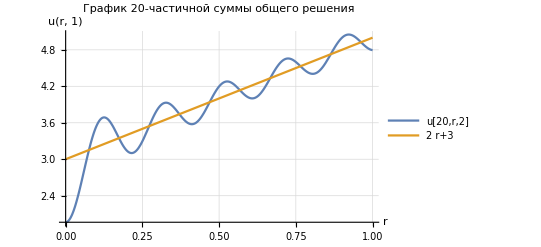

```mathematica
Plot[{ans,2r+3},{r,0,1},PlotRange->All, GridLines->Automatic,PlotLegends->{"u[20,r,2]",2r+3},AxesLabel->{"r","u(r, 1)"},PlotLabel->"График 20-частичной суммы общего решения"]
```

Исследуем аналитическое решение на сходимость и подберем оптимальное n для n-частичных сумм.
Для определения оптимального n был взят за основу алгоритм, написанный в 7-ой лабораторной работе.

```mathematica
f[r_]:=2r+3;
error = Abs[(MaxValue[{f[r], 0<=r<=1},r]-MinValue[{f[r],0<=r<=1},r])]*0.1;
```

```mathematica
iter = 1;
current = Maximize[{u[iter,r,h2]-f[r],0<=r<=1},r][[1]];
While[current>error,
iter+=1;
current = Maximize[{u[iter,r,h2]-f[r],0<=r<=1},r][[1]];
Print["n = ", iter, ". Максимальное отклонение при заданном n = ", current];
];
Print["Оптимальное количество n = ", iter]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained 2.51535×10^-16 and 7.6028×10^-16 for the integral and error estimates.

n = 2. Максимальное отклонение при заданном n = 1.71165

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained 2.51535×10^-16 and 7.6028×10^-16 for the integral and error estimates.

n = 3. Максимальное отклонение при заданном n = 3.09473

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained 2.51535×10^-16 and 7.6028×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

n = 4. Максимальное отклонение при заданном n = 1.04577

n = 5. Максимальное отклонение при заданном n = 2.38951

n = 6. Максимальное отклонение при заданном n = 0.822379

n = 7. Максимальное отклонение при заданном n = 2.00795

n = 8. Максимальное отклонение при заданном n = 0.703842

n = 9. Максимальное отклонение при заданном n = 1.76187

n = 10. Максимальное отклонение при заданном n = 0.626641

n = 11. Максимальное отклонение при заданном n = 1.58692

n = 12. Максимальное отклонение при заданном n = 0.570916

n = 13. Максимальное отклонение при заданном n = 1.45458

n = 14. Максимальное отклонение при заданном n = 0.528123

n = 15. Максимальное отклонение при заданном n = 1.35007

n = 16. Максимальное отклонение при заданном n = 0.493863

n = 17. Максимальное отклонение при заданном n = 1.26489

n = 18. Максимальное отклонение при заданном n = 0.300313

n = 19. Максимальное отклонение при заданном n = 1.19378

n = 20. Максимальное отклонение при заданном n = 0.441753

n = 21. Максимальное отклонение при заданном n = 1.13327

n = 22. Максимальное отклонение при заданном n = 0.421267

n = 23. Максимальное отклонение при заданном n = 1.08097

n = 24. Максимальное отклонение при заданном n = 0.403416

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

n = 25. Максимальное отклонение при заданном n = 1.0352

n = 26. Максимальное отклонение при заданном n = 0.387675

n = 27. Максимальное отклонение при заданном n = 0.994708

n = 28. Максимальное отклонение при заданном n = 0.373657

n = 29. Максимальное отклонение при заданном n = 0.958558

n = 30. Максимальное отклонение при заданном n = 0.361067

n = 31. Максимальное отклонение при заданном n = 0.926029

n = 32. Максимальное отклонение при заданном n = 0.349677

n = 33. Максимальное отклонение при заданном n = 0.896557

n = 34. Максимальное отклонение при заданном n = 0.339307

n = 35. Максимальное отклонение при заданном n = 0.869695

n = 36. Максимальное отклонение при заданном n = 0.329812

n = 37. Максимальное отклонение при заданном n = 0.845081

n = 38. Максимальное отклонение при заданном n = 0.321076

n = 39. Максимальное отклонение при заданном n = 0.822419

n = 40. Максимальное отклонение при заданном n = 0.313002

n = 41. Максимальное отклонение при заданном n = 0.801465

n = 42. Максимальное отклонение при заданном n = 0.30551

n = 43. Максимальное отклонение при заданном n = 0.782016

n = 44. Максимальное отклонение при заданном n = 0.298534

n = 45. Максимальное отклонение при заданном n = 0.763901

n = 46. Максимальное отклонение при заданном n = 0.292017

n = 47. Максимальное отклонение при заданном n = 0.746975

n = 48. Максимальное отклонение при заданном n = 0.28591

n = 49. Максимальное отклонение при заданном n = 0.731114

n = 50. Максимальное отклонение при заданном n = 0.280172

n = 51. Максимальное отклонение при заданном n = 0.71621

n = 52. Максимальное отклонение при заданном n = 0.274767

n = 53. Максимальное отклонение при заданном n = 0.702173

n = 54. Максимальное отклонение при заданном n = 0.269664

n = 55. Максимальное отклонение при заданном n = 0.688921

n = 56. Максимальное отклонение при заданном n = 0.264837

n = 57. Максимальное отклонение при заданном n = 0.676384

n = 58. Максимальное отклонение при заданном n = 0.26026

n = 59. Максимальное отклонение при заданном n = 0.6645

n = 60. Максимальное отклонение при заданном n = 0.255913

n = 61. Максимальное отклонение при заданном n = 0.653215

n = 62. Максимальное отклонение при заданном n = 0.251777

n = 63. Максимальное отклонение при заданном n = 0.64248

n = 64. Максимальное отклонение при заданном n = 0.247836

n = 65. Максимальное отклонение при заданном n = 0.632253

n = 66. Максимальное отклонение при заданном n = 0.244075

n = 67. Максимальное отклонение при заданном n = 0.622493

n = 68. Максимальное отклонение при заданном n = 0.240481

n = 69. Максимальное отклонение при заданном n = 0.613168

n = 70. Максимальное отклонение при заданном n = 0.237041

n = 71. Максимальное отклонение при заданном n = 0.604246

n = 72. Максимальное отклонение при заданном n = 0.233745

n = 73. Максимальное отклонение при заданном n = 0.595699

n = 74. Максимальное отклонение при заданном n = 0.230583

n = 75. Максимальное отклонение при заданном n = 0.587501

n = 76. Максимальное отклонение при заданном n = 0.227546

n = 77. Максимальное отклонение при заданном n = 0.579629

n = 78. Максимальное отклонение при заданном n = 0.224627

n = 79. Максимальное отклонение при заданном n = 0.572062

n = 80. Максимальное отклонение при заданном n = 0.221817

n = 81. Максимальное отклонение при заданном n = 0.564782

n = 82. Максимальное отклонение при заданном n = 0.21911

n = 83. Максимальное отклонение при заданном n = 0.55777

n = 84. Максимальное отклонение при заданном n = 0.2165

n = 85. Максимальное отклонение при заданном n = 0.551011

n = 86. Максимальное отклонение при заданном n = 0.213981

n = 87. Максимальное отклонение при заданном n = 0.544489

n = 88. Максимальное отклонение при заданном n = 0.211549

n = 89. Максимальное отклонение при заданном n = 0.538192

n = 90. Максимальное отклонение при заданном n = 0.209197

n = 91. Максимальное отклонение при заданном n = 0.532106

n = 92. Максимальное отклонение при заданном n = 0.206923

n = 93. Максимальное отклонение при заданном n = 0.526221

n = 94. Максимальное отклонение при заданном n = 0.204721

n = 95. Максимальное отклонение при заданном n = 0.520525

n = 96. Максимальное отклонение при заданном n = 0.202588

n = 97. Максимальное отклонение при заданном n = 0.515008

n = 98. Максимальное отклонение при заданном n = 0.200521

n = 99. Максимальное отклонение при заданном n = 0.509662

n = 100. Максимальное отклонение при заданном n = 0.198515

Оптимальное количество n = 100

При n = 100 погрешность не превышает  10% от разности максимального и минимального значений.

```mathematica
ansOptimal=u[100,r,2];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained 2.51535×10^-16 and 7.6028×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained -4.25007×10^-17 and 1.11254×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.70309}. NIntegrate obtained 7.50268×10^-17 and 1.57845×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

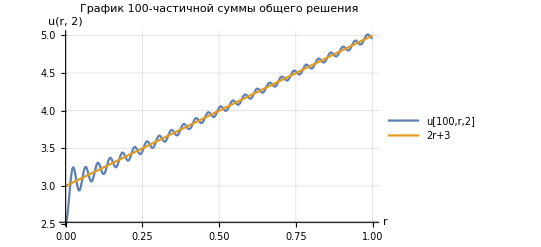

```mathematica
Plot[{ansOptimal,2r+3},{r,0,1},PlotRange->All, GridLines->Automatic,PlotLegends->{"u[100,r,2]","2r+3"},AxesLabel->{"r","u(r, 2)"},PlotLabel->"График 100-частичной суммы общего решения"]
```

Изобразим четыре частичные суммы аналитического решения и посмотрим, как они расположены друг относительно друга.

```mathematica
ans2=u[1,r,2];
ans3=u[20,r,2];
ans4=u[60,r,2];
ans5=u[100,r,2];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained 2.51535×10^-16 and 7.6028×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained -4.25007×10^-17 and 1.11254×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.70309}. NIntegrate obtained 7.50268×10^-17 and 1.57845×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained 2.51535×10^-16 and 7.6028×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained -4.25007×10^-17 and 1.11254×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.70309}. NIntegrate obtained 7.50268×10^-17 and 1.57845×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained 2.51535×10^-16 and 7.6028×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.9999923014314252000705508533623389055833285965491086244583129883}. NIntegrate obtained -4.25007×10^-17 and 1.11254×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {1.70309}. NIntegrate obtained 7.50268×10^-17 and 1.57845×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

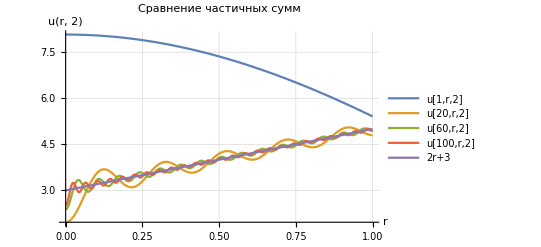

```mathematica
Plot[{ans2,ans3,ans4,ans5,2r+3},{r,0,1},PlotRange->All, GridLines->Automatic,PlotLegends->{"u[1,r,2]","u[20,r,2]","u[60,r,2]","u[100,r,2]","2r+3"},AxesLabel->{"r","u(r, 2)"},PlotLabel->"Сравнение частичных сумм"]
```

### Вывод

В ходе выполнения лабораторной работы было решено численно и аналитически уравнение Лапласа в цилиндрической системе координат.
	1) Для численного решения использовались функции встроенные в Wolfram Mathematica, такие так Laplacian[], NDSolveValue[], DirichletCondition[].
	2) Для построения аналитического решения были использованы формулы полученные на лекции.
	Кроме этого в данной работе было построено сечение аналитического решения плоскостью z=2, а также подобрано оптимальное n для n-частичных сумм в аналитическом решении. Все результаты представлены на графиках.
	Также были изучены новые функции:  Laplacian[], DirichletCondition[], Cylinder[].